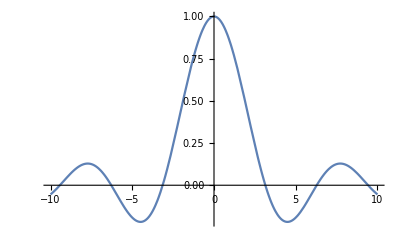

```mathematica
Plot[Sinc[x],{x,-10,10}]
```

```mathematica
(* ... Let's define those generalized Binomial Coefficients, and see how they look when plotted in 3d! :) This may help us extend our intuition to the Multinomial (n-D) case. *)
genBinom[y_,x_]:=Module[{y0=y,x0=x},Gamma[1+y0]/(Gamma[1+x0]*Gamma[1+y0-x0])]
```

```mathematica
Plot3D[genBinom[y,x],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
genBinom[4,2]
```

6

```mathematica
(* Hmmm... okay. *)
```

```mathematica
genBinom[0,2]
```

0

```mathematica
N[genBinom[Pi,-3]]
```

0.

```mathematica
(* ---------------- 3-17-22 ----------------- *)
(* OKAY.. now, it's time for me to start making "grand conjectures" (lol). To do this, let's first experiment a lil bit. *)
```

```mathematica
(* Take the integral of Salwinski's multinomial coefficients for y > -1:
```

```mathematica
(* DEFINITION: *)
(* we already have genBinom...*)
```

```mathematica
genMultinom[n_,ni__]:=Module[{n0=n, args= ni},
(Gamma[n+1])/(Product[Gamma[i+1],{i,args}])
]
```

```mathematica
genMultinom[7,{2,2,3}]
```

210

```mathematica
Multinomial[2,2,3]
```

210

```mathematica
N[genMultinom[3*Pi,{Pi,2*Pi}]]
```

107.725

```mathematica
(* Yep it works. Technically you should make it throw an error if the sum over args doesn't equal n. !!! *)
```

```mathematica
genMultinom[7,{1,2,6}]
```

7/2

```mathematica
N[genMultinom[-2*Pi,{2*Pi,-Pi,-3*Pi}]]
```

0.164456

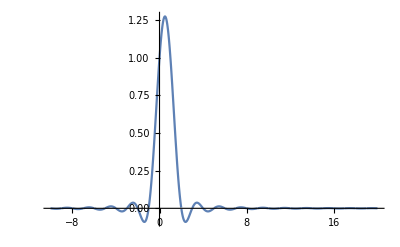

```mathematica
(* Now, let's see what we can do with plotting and integration... First, over  the binomial coefficients... Salwinski's Integral: *)
(* Must have y > -1 ... *)
Plot[genBinom[1,x],{x,-10,20},PlotRange->Full]
```

```mathematica
Maximize[genBinom[1,x],x]
```

Maximize::incs: Warning: Maximize was unable to prove that the result is a global maximum.

Maximize::fexp: Warning: Maximize used FunctionExpand to transform the problem. Since FunctionExpand transformation rules are only generically correct, the result may not be a global maximum.

{4/π,{x→1/2}}

```mathematica
(* Now, integrate this b... *)
NIntegrate[genBinom[1,x],{x,-Infinity,Infinity}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {68.0534}. NIntegrate obtained 1.99959 and 0.00161939 for the integral and error estimates.

1.99959

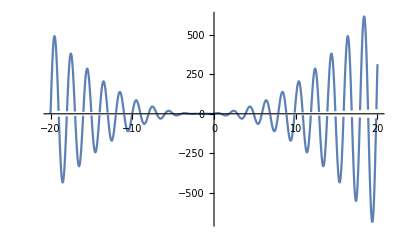

```mathematica
(* ... This DOES equal 2^y = 2, as expected! :D *)
(* NOw, how does it break down in the negatives...? *)
Plot[genBinom[-Pi,x],{x,-20,20},PlotRange->Full]
```

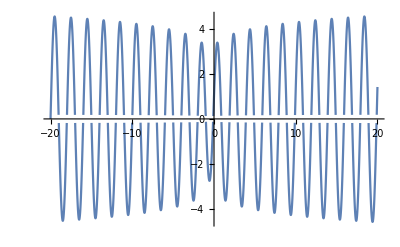

```mathematica
(* ... ooh, so it diverges... interesting. And the "breakaway value" for this divergence is:*)
Plot[genBinom[-1.1,x],{x,-20,20},PlotRange->Full]
```

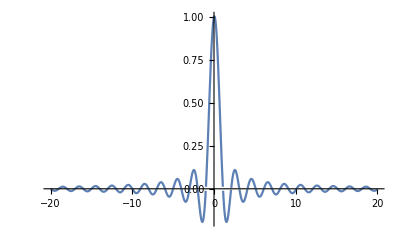

```mathematica
Plot[genBinom[+0.1,x],{x,-20,20},PlotRange->Full]
```

```mathematica
NIntegrate[genBinom[-0.9,x],{x,-Infinity,Infinity}]
```

NIntegrate::inumri: The integrand 9.51351/(Gamma[0.1-x] Gamma[1+x]) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-320.369,-205.055}}.

NIntegrate[genBinom[-0.9,x],{x,-∞,∞}]

```mathematica
(* Results inconclusive. Oh well... For ours, we'll start by restricting our n to be positive, then... Until we're ablle to get some asymptotics / convergence stuff nailed down, which should be a GOAL (!) *)

(* ===================================================================================================================== *)
```

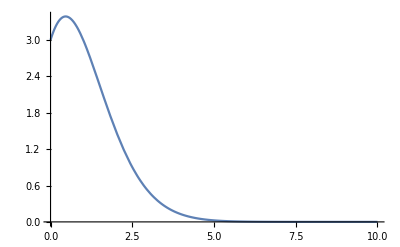

```mathematica
(* We'll start by plotting some tingz *)
(* Let's restrict our n to be positive real. *)
(* TRINOMIAL *)
Plot[genMultinom[3,{x,2}],{x,0,10}]
```

```mathematica
Plot3D[genMultinom[3,{x,y}],{x,-2,10},{y,-2,10}]
```

-Graphics3D-

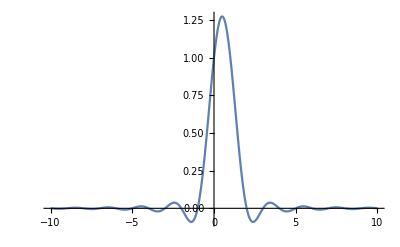

```mathematica
Plot[genMultinom[1,{x,1-x}],{x,-10,10},PlotRange->Full] (* Recovered the other one. *)
```

```mathematica
Plot3D[genMultinom[1,{x,y,1-x-y}],{x,-2,10},{y,-2,10}]
```

-Graphics3D-

-Graphics3D-

```mathematica
(* Wild shot *)
p = InfinitePlane[{{3,0,0},{0,3,0},{0,0,3}}]
NIntegrate[genMultinom[3,{x,y,z}],{x,y,z}∈p]
```

InfinitePlane[{{3,0,0},{0,3,0},{0,0,3}}]

NIntegrate::inumri: The integrand 6/(Gamma[1+x] Gamma[1+y] Gamma[1+z]) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.0000453999,0.035674},{0,1}}.

NIntegrate[genMultinom[3,{x,y,z}],{x,y,z}∈p]

```mathematica
(* ... *)
(* Try one more thing...  Then we're done for today... *)
n=3;
NIntegrate[NIntegrate[(Gamma[n+1])/(Gamma[x+1]*Gamma[y+1]*Gamma[n-x-y+1])*Sqrt[3],{y,0,x}],{x,0,n}]
```

NIntegrate::nlim: y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

17.7748

```mathematica
NumberForm[17.77478076292977,16]
```

17.77478076292977

```mathematica
(* Try to normalize? *)
27/"17.77478076292977"
```

1.51901

```mathematica
NumberForm[1.5190060772119285,16]
```

1.519006077211928

```mathematica
NumberForm[17.77478076292977,16]
```

17.77478076292977

```mathematica
n=1;
NIntegrate[NIntegrate[(Gamma[n+1])/(Gamma[x+1]*Gamma[y+1]*Gamma[n-x-y+1])*Sqrt[3],{y,-Infinity,Infinity}],{x,-Infinity,Infinity}]
```

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumr: The integrand (√3)/(Gamma[1+x] Gamma[2-x-y] Gamma[1+y]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumr: The integrand (√3)/(Gamma[1-x] Gamma[2+x-y] Gamma[1+y]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate[NIntegrate[(Gamma[n+1] √3)/(Gamma[x+1] Gamma[y+1] Gamma[n-x-y+1]),{y,-∞,∞}],{x,-∞,∞}]

```mathematica
(* Is theh reasson it makes no sense because now addition is "no longer commutative?" *)
(* E.g (3+2)^sqrt(2) = ... if we're taking (x+y)^r, we require that |x| > |y| in order for it to converge!*)
N[(3 + 2)^Sqrt[2]]
```

9.73852

```mathematica
N[Sum[genBinom[Sqrt[2],k]*3^(Sqrt[2]-k)*2^k,{k,0,100}]]
```

9.73852

```mathematica
(* Okay, now switch the order! *)
N[Sum[genBinom[Sqrt[2],k]*2^(Sqrt[2]-k)*3^k,{k,0,100}]]
```

3.74016×10^12

```mathematica
(* Yeah then it blows up. *)
(* What about if they're equal in magnitude??? *)
N[(2+2)^Sqrt[2]]
```

7.10299

```mathematica
N[Sum[genBinom[Sqrt[2],k]*2^(Sqrt[2]-k)*2^k,{k,0,105}]]
```

7.10299

```mathematica
NumberForm[7.103000949008859,16]
```

7.103000949008859

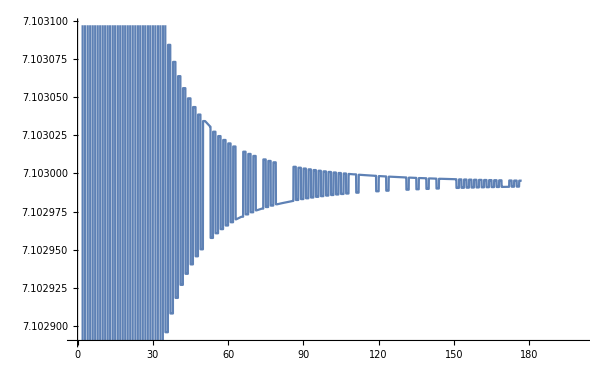

```mathematica
Plot[N[Sum[genBinom[Sqrt[2],k]*2^(Sqrt[2]-k)*2^k,{k,0,x}]],{x,0,200}]
```

```mathematica
(* What about if r is NEGATIVE? *)
```

```mathematica
N[(3 + 2)^-Sqrt[2]]
```

0.102685

```mathematica
N[Sum[genBinom[-Sqrt[2],k]*3^(-Sqrt[2]-k)*2^k,{k,0,100}]]
```

0.102685

```mathematica
N[Sum[genBinom[-Sqrt[2],k]*2^(-Sqrt[2]-k)*3^k,{k,0,100}]]
```

6.9863×10^17

```mathematica
(* Yep, still converges for one, diverges for the other! *)
(* Now, fractinal r??? *) (* Pos and neg?*)
```

```mathematica
N[(3 + 2)^(1/2)]
N[(3 + 2)^(-1/2)]
```

2.23607

0.447214

```mathematica
N[Sum[genBinom[1/2,k]*3^(1/2-k)*2^k,{k,0,100}]]
N[Sum[genBinom[-1/2,k]*3^(-1/2-k)*2^k,{k,0,100}]]
```

2.23607

0.447214

```mathematica
N[Sum[genBinom[1/2,k]*2^(1/2-k)*3^k,{k,0,100}]]
N[Sum[genBinom[-1/2,k]*2^(-1/2-k)*3^k,{k,0,100}]]
```

-9.70945×10^13

9.70009×10^15

```mathematica
(* straggler cases: Same 2 summands, fractional r and or negative r *)
N[(2+ 2)^(-1/2)]
N[(2+ 2)^(-Sqrt[2])]
```

0.5

0.140786

```mathematica
N[Sum[genBinom[-1/2,k]*2^(-1/2-k)*2^k,{k,0,1000}]]
N[Sum[genBinom[-Sqrt[2],k]*2^(-Sqrt[2]-k)*2^k,{k,0,100}]]
```

0.506305

-1.29764

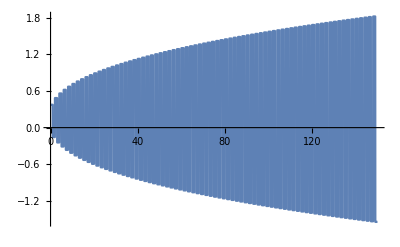

```mathematica
Plot[N[Sum[genBinom[-Sqrt[2],k]*2^(-Sqrt[2]-k)*2^k,{k,0,x}]],{x,0,150}]
```

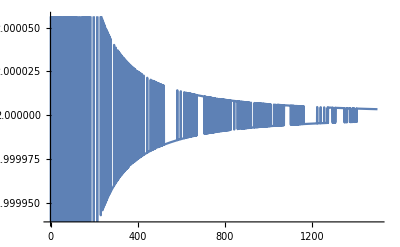

```mathematica
(* OKAY, so conjecture: If your summands are equal, it diverges if your r is < -1. *)
Plot[N[Sum[genBinom[1/2,k]*2^(1/2-k)*2^k,{k,0,x}]],{x,0,1500}]
```

```mathematica
(* Now... what about with negative summands? *)
N[(-2+ 2)^(Sqrt[2])]
```

0.

```mathematica
N[Sum[genBinom[Sqrt[2],k]*(2)^(Sqrt[2]-k)*(-2)^k,{k,0,100}]]
```

-0.00107937

```mathematica
(* =============================================== SWITCHING GEARS ==================================================== *)
(* Now let's investigate the generalized sine and cosine that Prof. Reznick was talking about... *)
 (*x^k/k!-x^(k+n}/(k+n)!+x^(k+2n}/(k+2n)!-x^(k+3n}/(k+3n)!+…  f(2,0)=cos and f(2,1)=sin *)
```

```mathematica
f[n_,k_,x_]:=Module[{x0=x,n0=n,k0=k},Sum[(-1)^i*x0^(k0+i*n0)/(k0+i*n0),{i,0,10000}]]
```

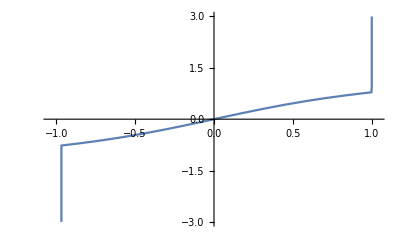

```mathematica
Plot[f[2,1,x],{x,-Pi,Pi},PlotRange->{-3,3}]
```

```mathematica
(* ========= 3-19: A rehash of yesteerday's highlights/... *)
N[(2+ 2)^(Sqrt[2])]
```

7.10299

```mathematica
N[Sum[genMultinom[Sqrt[2],{k,Sqrt[2]-k}]*(2)^Sqrt[2],{k,0,100}]]
```

7.103

```mathematica
NumberForm[7.103000949008859,16]
```

7.103000949008859